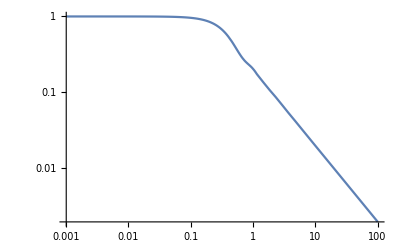

```mathematica
LogLogPlot[HypergeometricPFQ[{1/2},{3/2,2},-(q*10/2)^2],{q,0.001,101}]
```

```mathematica
Asymptotic[HypergeometricPFQ[{1/2},{3/2,2},-(q*B/2)^2],q->Infinity,Assumptions->B>0 && q>0]
```

2/(B q)

```mathematica
Series[HypergeometricPFQ[{1/2},{3/2,2},-(q*B/2)^2],{q,0,8},Assumptions->B>0 && q>0]
```

1-(B^2 q^2)/24+(B^4 q^4)/960-(B^6 q^6)/64512+(B^8 q^8)/6635520+O[q]^9

```mathematica
FullSimplify[Asymptotic[HypergeometricPFQ[{1/2,1+B^2/sB^2/2,3/2+B^2/sB^2/2},{3/2,2},-(q*sB^2/B)^2],q->Infinity,Assumptions->B>0 && sB>0&& q>0&& B > sB]]
```

(2 B)/(q (B^2+sB^2))

```mathematica
CForm[%29]
```

((2*B*Power(q,2))/(Power(B,2) + Power(sB,2)) + 
     (Power(B/q,Power(B,2)/Power(sB,2))*
        ((2*B*Gamma(1 - Power(B,2)/(2.*Power(sB,2)))*
             Gamma((1 + Power(B,2)/Power(sB,2))/2.))/
           (Power(sB,2)*(Power(B,2) + 2*Power(sB,2))) + 
          (q*Gamma(1 + Power(B,2)/(2.*Power(sB,2)))*
             Gamma(-(Power(B,2) + Power(sB,2))/(2.*Power(sB,2))))/
           (Power(B,2) + Power(sB,2)))*
        Sin((Power(B,2)*Pi)/Power(sB,2)))/
      (Power(Pi,1.5)*Power(sB,(2*Power(B,2))/Power(sB,2))))/
   Power(q,3)

```mathematica
x:=q*sB^2/B
```

```mathematica
Simplify[Normal[Series[HypergeometricPFQ[{1/2,1+B^2/sB^2/2,3/2+B^2/sB^2/2},{3/2,2},-(q*sB^2/B)^2],{q,0,4},Assumptions->B>0 && q>0]]]
```

1-(q^2 (B^2+2 sB^2) (B^2+3 sB^2))/(24 B^2)+(q^4 (B^2+2 sB^2) (B^2+3 sB^2) (B^2+4 sB^2) (B^2+5 sB^2))/(960 B^4)

```mathematica
Integrate[Sinc[x*q*c/2]^2,{x,-1,1}]
```

(4 (-1+Cos[c q]+c q SinIntegral[c q]))/(c^2 q^2)

```mathematica
FullSimplify[Normal[Series[HypergeometricPFQ[{1/2,1+B^2/sB^2/2,3/2+B^2/sB^2/2},{3/2,2},-(q*sB^2/B)^2],{q,Infinity,1},Assumptions->B>0 && q>0&& sB>0&& B > sB]],Assumptions->B>0 && q>0&& sB>0&& B > sB]
```

1/q^3((2 B q^2)/(B^2+sB^2)+1/π^(3/2)(B/q)^(B^2/sB^2) sB^(-(2 B^2)/sB^2) ((2 B Gamma[1-B^2/(2 sB^2)] Gamma[1/2 (1+B^2/sB^2)])/(sB^2 (B^2+2 sB^2))+(q Gamma[1+B^2/(2 sB^2)] Gamma[-(B^2+sB^2)/(2 sB^2)])/(B^2+sB^2)) Sin[(B^2 π)/sB^2])

```mathematica
CForm[%]
```

((2*B*Power(q,2))/(Power(B,2) + Power(sB,2)) + 
     (Power(B/q,Power(B,2)/Power(sB,2))*
        ((2*B*Gamma(1 - Power(B,2)/(2.*Power(sB,2)))*
             Gamma((1 + Power(B,2)/Power(sB,2))/2.))/
           (Power(sB,2)*(Power(B,2) + 2*Power(sB,2))) + 
          (q*Gamma(1 + Power(B,2)/(2.*Power(sB,2)))*
             Gamma(-(Power(B,2) + Power(sB,2))/(2.*Power(sB,2))))/
           (Power(B,2) + Power(sB,2)))*
        Sin((Power(B,2)*Pi)/Power(sB,2)))/
      (Power(Pi,1.5)*Power(sB,(2*Power(B,2))/Power(sB,2))))/
   Power(q,3)

```mathematica
Ribbon[q_,B_,sB_]:=HypergeometricPFQ[{1/2,1+B^2/sB^2/2,3/2+B^2/sB^2/2},{3/2,2},-(q*sB^2/B)^2]
```

```mathematica
Series[Ribbon[q,B,sB],{sB,0,4}]
```

HypergeometricPFQ[{1/2,1+B^2/(2 sB^2),3/2+B^2/(2 sB^2)},{3/2,2},-(q^2 sB^4)/B^2]

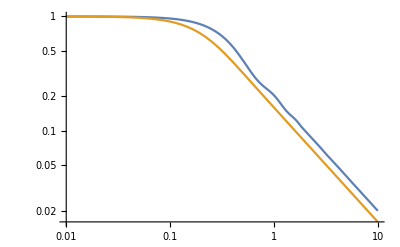

```mathematica
LogLogPlot[{Ribbon[q,10,1/100],Ribbon[q,10,5]},{q,0.01,10}]
```

```mathematica
Series[(1-Re[(1+I*q*sA^2/A)^(-(a/sA)^2)])/q^2,{q,0,4}]
```

Re[(1+(ⅈ q sA^2)/A)^(-a^2/sA^2)] (-1/q^2+O[q]^5)+(1/q^2+O[q]^5)

```mathematica
Limit[(1-Re[(1+I*q*sA^2/A)^(-(A/sA)^2)])/q^2,q->0,Assumptions->sA>0&&A>0]
```

Limit[(1-Re[(1+(ⅈ q sA^2)/A)^(-A^2/sA^2)])/q^2,q→0,Assumptions→sA>0&&A>0]

```mathematica
shortP[q_,A_,sA_]:=(1-Re[(1+(ⅈ q sA^2)/A)^(-A^2/sA^2)])/q^2
```

```mathematica
N[shortP[0.0001,10,11]]
```

```mathematica
fG[a_,a0_,sa_]:=Exp[-a0*a/sa^2]*(a0*a/sa^2)^((a0/sa)^2)/(a*Gamma[a0^2/sa^2])
```

```mathematica
Integrate[a^2*fG[a,a0,sa],{a,0,Infinity},Assumptions->a0>0&&sa>0]
```

a0^2+sa^2

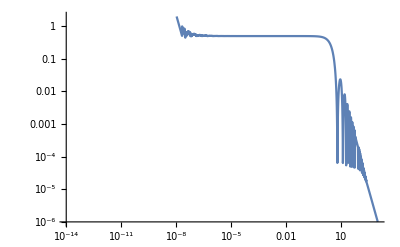

```mathematica
LogLogPlot[shortP[q,1,1/10^2],{q,10^(-14),10^3}]
```